```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zitko/Dropbox/notes/2021_chi/ed-tau

```mathematica
<<sneg`;
```

sneg 1.252 Copyright (C) 2002-2019 Rok Zitko

a::shdw: Symbol a appears in multiple contexts {Sneg`,Global`}; definitions in context Sneg` may shadow or be shadowed by other definitions.

```mathematica
snegfermionoperators[c,d];
snegrealconstants[nu];
```

```mathematica
n=2;
ddd=2/n;
bz=qsbasisvc[{c[1],c[2],d[]}];
bz=Map[{#[[1]]+{n+1,0},#[[2]]}&,bz];
```

```mathematica
-1.+ddd/2
```

-0.5

```mathematica
ClearAll[ϵ];U=.;nu=.;t=.;V=.;
H=U/2 pow[number[d]-nu, 2]+U/2-U/2nu^2+Sum[ϵ[i] number[c[i]],{i,n}]+V Sum[nc[c[CR,i,UP],c[CR,i,DO],c[AN,j,DO],c[AN,j,UP]],{i,n},{j,n}]+t Sum[hop[c[i],d[]],{i,n}]//Expand
ϵ[1]=-1/2;
ϵ[2]=1/2;
U=10;
gamma=1;
V=Sqrt[2. gamma/Pi]
t=V/Sqrt[n]
α=1;
V=-α ddd;
H
mats=makematricesbzvc[H,bz]
```

U/2+t c_(1↓)^†·d_↓^+t c_(1⇑)^†·d_⇑^+t c_(2↓)^†·d_↓^+t c_(2⇑)^†·d_⇑^+t d_↓^†·c_(1↓)^+t d_↓^†·c_(2↓)^+1/2 U d_↓^†·d_↓^-nu U d_↓^†·d_↓^+t d_⇑^†·c_(1⇑)^+t d_⇑^†·c_(2⇑)^+1/2 U d_⇑^†·d_⇑^-nu U d_⇑^†·d_⇑^-V c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^-V c_(1↓)^†·c_(1⇑)^†·c_(2↓)^·c_(2⇑)^-V c_(2↓)^†·c_(2⇑)^†·c_(1↓)^·c_(1⇑)^-V c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^-U d_↓^†·d_⇑^†·d_↓^·d_⇑^+c_(1↓)^†·c_(1↓)^ ϵ[1]+c_(1⇑)^†·c_(1⇑)^ ϵ[1]+c_(2↓)^†·c_(2↓)^ ϵ[2]+c_(2⇑)^†·c_(2⇑)^ ϵ[2]

0.797885

0.56419

5-1/2 c_(1↓)^†·c_(1↓)^+0.56419 c_(1↓)^†·d_↓^-1/2 c_(1⇑)^†·c_(1⇑)^+0.56419 c_(1⇑)^†·d_⇑^+1/2 c_(2↓)^†·c_(2↓)^+0.56419 c_(2↓)^†·d_↓^+1/2 c_(2⇑)^†·c_(2⇑)^+0.56419 c_(2⇑)^†·d_⇑^+0.56419 d_↓^†·c_(1↓)^+0.56419 d_↓^†·c_(2↓)^+5 d_↓^†·d_↓^-10 nu d_↓^†·d_↓^+0.56419 d_⇑^†·c_(1⇑)^+0.56419 d_⇑^†·c_(2⇑)^+5 d_⇑^†·d_⇑^-10 nu d_⇑^†·d_⇑^+c_(1↓)^†·c_(1⇑)^†·c_(1↓)^·c_(1⇑)^+c_(1↓)^†·c_(1⇑)^†·c_(2↓)^·c_(2⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(1↓)^·c_(1⇑)^+c_(2↓)^†·c_(2⇑)^†·c_(2↓)^·c_(2⇑)^-10 d_↓^†·d_⇑^†·d_↓^·d_⇑^

{{{0,0},{{5}}},{{1,1/2},{{10.-10 nu,0.56419,0.56419},{0.56419,5.5,0.},{0.56419,0.,4.5}}},{{2,0},{{25.-20 nu,0.797885,0.797885,0.,0.,0.},{0.797885,-10. (-1.05+nu),0.,0.797885,0.56419,0.},{0.797885,0.,-10. (-0.95+nu),0.,0.56419,0.797885},{0.,0.797885,0.,5.,0.,-1.},{0.,0.56419,0.56419,0.,5.,0.},{0.,0.,0.797885,-1.,0.,3.}}},{{2,1},{{10.5-10 nu,0.,-0.56419},{0.,9.5-10 nu,0.56419},{-0.56419,0.56419,5.}}},{{3,1/2},{{25.5-20 nu,0.,-0.56419,-0.398942,0.,-0.690988,0.,0.},{0.,24.5-20 nu,0.,-0.398942,-0.56419,0.690988,0.,0.},{-0.56419,0.,10.-10 nu,0.,-1.,0.,0.56419,0.},{-0.398942,-0.398942,0.,-10. (-1.+nu),0.,0.,-0.398942,-0.398942},{0.,-0.56419,-1.,0.,8.-10 nu,0.,0.,0.56419},{-0.690988,0.690988,0.,0.,0.,-10. (-1.+nu),0.690988,-0.690988},{0.,0.,0.56419,-0.398942,0.,0.690988,4.5,0.},{0.,0.,0.,-0.398942,0.56419,-0.690988,0.,3.5}}},{{3,3/2},{{-10 (-1+nu)}}},{{4,0},{{25.-20 nu,0.,-1.,0.797885,0.,0.},{0.,-20. (-1.25+nu),0.,-0.56419,-0.56419,0.},{-1.,0.,23.-20 nu,0.,0.797885,0.},{0.797885,-0.56419,0.,-10. (-0.95+nu),0.,0.797885},{0.,-0.56419,0.797885,0.,-10. (-0.85+nu),0.797885},{0.,0.,0.,0.797885,0.797885,3.}}},{{4,1},{{25.-20 nu,-0.56419,0.56419},{-0.56419,9.5-10 nu,0.},{0.56419,0.,8.5-10 nu}}},{{5,1/2},{{24.5-20 nu,0.,-0.56419},{0.,23.5-20 nu,-0.56419},{-0.56419,-0.56419,8.-10 nu}}},{{6,0},{{23-20 nu}}}}

```mathematica
matn=matrixrepresentationvc[number[d[]],bz[[5,2]]];
MatrixForm[matn]
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
ClearAll[calc,calc0];
sub=5;
calc0[x_]:=calc0[x]=Module[{},
nu=x;
eps=U(1/2-x);
{qn,hh}=mats[[sub]];
bas=bz[[5,2]];
{val,vec}=Transpose@Sort@Transpose@Eigensystem[hh];
ω0j=val-First[val];
gij=vec.matn.ConjugateTranspose[vec];
χ=Sum[gij[[1,j]]^2(-1/(ω0j[[j]]-z)-1/(ω0j[[j]]+z)),{j,2,8}];
χ1=Sum[gij[[1,j]]^2(-1/(ω0j[[j]]-z)),{j,1,8}];
χ2=Sum[gij[[1,j]]^2(-1/(ω0j[[j]]+z)),{j,1,8}];
{eps,val,ω0j,gij,χ}
];
calc[x_]:=Module[{},
{eps,val,ω0j,gij,χ}=calc0[x];
];
```

```mathematica
calc[1]
eps
val
ω0j
MatrixForm[gij]
ωr=0.25;
η=0.1;
Re[χ]/.z->ωr
Re[χ]/.z->ωr+η I
Re[χ1]/.z->ωr+η I
Re[χ2]/.z->ωr+η I
%+%%
```

-5

{-2.51293,-0.443828,-0.140417,0.341,3.69239,4.54993,4.8179,5.69595}

{0.,2.0691,2.37251,2.85393,6.20532,7.06286,7.33083,8.20888}

(0.997624 | -0.00381294 | 0.0200803 | 0.000204141 | -0.0958772 | 0.0307707 | 0.0659822 | -0.0193301
-0.00381294 | 0.981939 | 0.00688488 | -0.004075 | -0.180706 | 0.201704 | -0.0535184 | 0.108091
0.0200803 | 0.00688488 | 0.993664 | -0.0093159 | 0.101549 | 0.124322 | 0.0214891 | -0.062364
0.000204141 | -0.004075 | -0.0093159 | 0.998374 | -0.00667669 | 0.0536524 | -0.0569611 | 0.0484652
-0.0958772 | -0.180706 | 0.101549 | -0.00667669 | 0.0776811 | -0.163098 | -0.113157 | -0.1389
0.0307707 | 0.201704 | 0.124322 | 0.0536524 | -0.163098 | 1.00314 | 0.936587 | 0.167788
0.0659822 | -0.0535184 | 0.0214891 | -0.0569611 | -0.113157 | 0.936587 | 1.02324 | -0.202474
-0.0193301 | 0.108091 | -0.062364 | 0.0484652 | -0.1389 | 0.167788 | -0.202474 | 1.92434)

-0.00487432

-0.00487257

3.42937

-3.43424

-0.00487257

```mathematica
E0=First[val];
ψ0=First[vec];
ω0=E0+ωr
ω0p=E0-ωr
```

-2.26293

-2.76293

```mathematica
id=IdentityMatrix[Dimensions[hh]];
ndmat=matrixrepresentationop[number[d],bas];
(* A1 *)
mat=Chop[ConjugateTranspose[ndmat].Inverse[(E0+ωr+I η)id-hh].ndmat];
A1=conj[ψ0].(mat.ψ0)
(* A2 *)
mat=Chop[ConjugateTranspose[ndmat].Inverse[(E0-ωr-I η)id-hh].ndmat];
A2=conj[ψ0].(mat.ψ0)
A1+A2
```

3.42937-1.37281 ⅈ

-3.43424+1.3728 ⅈ

-0.00487257-8.54647×10^-6 ⅈ

```mathematica
Norm[ψ0]==1
ψA=ndmat.ψ0
```

True

{-0.0472716,-0.153603,-0.376567,0.00266717,-0.917544,0.0318376,0.,0.}

```mathematica
(* eq20 *)
YA=-η Inverse[MatrixPower[(E0+ωr)id-hh,2]+η^2 id].ψA
XA=(hh-ω0 id).YA/η
ReGA=ψA.XA
%==Re[A1]
```

{0.0325981,0.105869,0.518192,-0.00327934,1.26258,-0.0437234,-0.0375037,-0.123429}

{-0.0778104,-0.252522,-1.29499,0.0154141,-3.15592,0.110599,0.0981967,0.325433}

3.42937

True

```mathematica
ψB=(-hh+ω0 id).ψA;
ψBp=(-hh+ω0p id).ψA;
Hsq=MatrixPower[hh-ω0 id ,2];
Eigenvalues[Hsq]
Hsqp=MatrixPower[hh-ω0p id,2];
Eigenvalues[Hsqp]
```

{63.3437,50.1382,46.4151,35.4658,6.78044,4.50505,3.30913,0.0625}

{71.5526,57.469,53.4779,41.6712,9.63437,6.87756,5.37823,0.0625}

```mathematica
ψAτ[τ_]:=MatrixExp[-τ Hsq].ψA
{ψB.ψAτ[0],ψB.ψAτ[0.01],ψB.ψAτ[0.1],ψB.ψAτ[1]}
ψApτ[τ_]:=MatrixExp[-τ Hsqp].ψA
{ψBp.ψApτ[0],ψBp.ψApτ[0.01],ψBp.ψApτ[0.1],ψBp.ψApτ[1]}
```

{0.152935,0.18511,0.244849,0.233728}

{-0.352334,-0.312974,-0.248875,-0.23374}

```mathematica
ψA.ψA
```

1.01054

```mathematica
ψA.(hh-ω0 id).ψA
ψA.MatrixPower[(hh-ω0 id),2].ψA
```

-0.152935

0.675986

```mathematica
ψA.(hh-ω0p id).ψA
ψA.MatrixPower[(hh-ω0p id),2].ψA
```

0.352334

0.775686

```mathematica
(* debug evolution *)
ψAτ[0.01]
%.%
ψApτ[0.01]
%.%
```

{-0.0364345,-0.125313,-0.376301,-0.00330371,-0.91684,0.0315694,0.0101057,0.0255788}

1.00099

{-0.0354731,-0.122045,-0.376276,-0.00370018,-0.916753,0.031499,0.0112476,0.029304}

1.00016

```mathematica
(* debug exp[H] *)
ψA.MatrixExp[-0.02hh].ψA
ψA.MatrixExp[-0.02(hh-ω0p id)].ψA
```

1.06066

1.00364

```mathematica
(* eq 26 *)
ψI=Inverse[MatrixPower[hh-ω0 id ,2]+η^2 id].ψA
%==(-1/η)YA
```

{-0.325981,-1.05869,-5.18192,0.0327934,-12.6258,0.437234,0.375037,1.23429}

True

```mathematica
(* eq 27 *)
XA2=(-hh+ω0 id).ψI
%==XA
```

{-0.0778104,-0.252522,-1.29499,0.0154141,-3.15592,0.110599,0.0981967,0.325433}

True

```mathematica
(* eq. 28 *)
-ψA.(hh-ω0 id).ψI
ψB.ψI
```

3.42937

3.42937

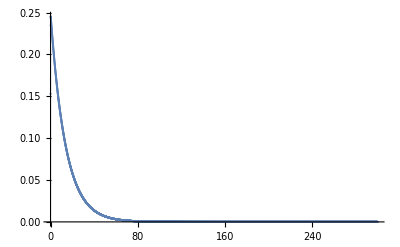

3.42922

-0.000147051

```mathematica
tab=Table[{τ,Exp[-η^2 τ] ψB.ψAτ[τ]},{τ,0,300,0.05}];
ListPlot[tab,PlotRange->All]
f=Interpolation[tab];
NIntegrate[f[x],{x,0,300},MaxRecursion->20]
%-Re[A1]
```

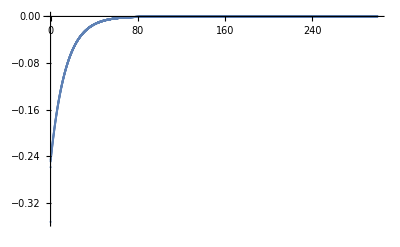

-3.43446

-0.000222281

```mathematica
tab=Table[{τ,Exp[-η^2 τ] ψBp.ψApτ[τ]},{τ,0,300,0.05}];
ListPlot[tab,PlotRange->All]
f=Interpolation[tab];
NIntegrate[f[x],{x,0,300},MaxRecursion->20]
%-Re[A2]
```

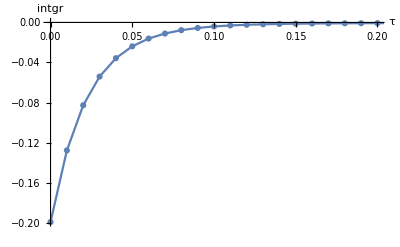

tau.pdf

-0.00484542

-0.00557181

```mathematica
tab=Table[{τ,Exp[-η^2 τ]( ψB.ψAτ[τ]+ψBp.ψApτ[τ])},{τ,0,0.5,0.01}];
ListPlot[tab,PlotRange->{{0,0.2},All},AxesLabel->{"τ","intgr"},LabelStyle->Larger,Joined->True,Mesh->True]
Export["tau.pdf",%]
f=Interpolation[tab];
res=NIntegrate[f[x],{x,0,0.5},MaxRecursion->20]
relerror=(res-Re[A1+A2])/Re[A1+A2]
```

```mathematica
Re[A1+A2]
resDMRG=-0.004870128
(resDMRG-Re[A1+A2])/Re[A1+A2]
```

-0.00487257

-0.00487013

-0.000501157

```mathematica
TableForm[tab]
```

0. | -0.199399
0.01 | -0.127851
0.02 | -0.0827473
0.03 | -0.0540794
0.04 | -0.0357122
0.05 | -0.0238531
0.06 | -0.0161377
0.07 | -0.0110803
0.08 | -0.00773977
0.09 | -0.00551572
0.1 | -0.00402238
0.11 | -0.00301023
0.12 | -0.00231688
0.13 | -0.001836
0.14 | -0.0014976
0.15 | -0.00125534
0.16 | -0.00107841
0.17 | -0.000946225
0.18 | -0.000844949
0.19 | -0.000765254
0.2 | -0.000700814
0.21 | -0.00064732
0.22 | -0.000601819
0.23 | -0.000562272
0.24 | -0.000527264
0.25 | -0.000495803
0.26 | -0.000467183
0.27 | -0.0004409
0.28 | -0.000416586
0.29 | -0.000393965
0.3 | -0.000372832
0.31 | -0.000353023
0.32 | -0.000334412
0.33 | -0.000316894
0.34 | -0.000300382
0.35 | -0.000284802
0.36 | -0.000270089
0.37 | -0.000256187
0.38 | -0.000243043
0.39 | -0.000230611
0.4 | -0.000218849
0.41 | -0.000207717
0.42 | -0.00019718
0.43 | -0.000187203
0.44 | -0.000177754
0.45 | -0.000168804
0.46 | -0.000160325
0.47 | -0.000152292
0.48 | -0.000144678
0.49 | -0.000137462
0.5 | -0.000130622

```mathematica
Exp[-η^2 0.5]
```

0.995012